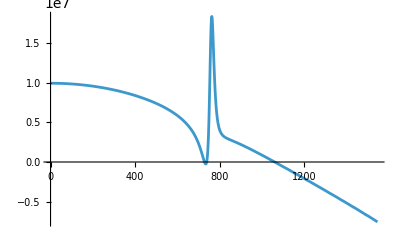

```mathematica
SetDirectory[NotebookDirectory[]];
Re1=Flatten[Import["Re.dat"]];
Im1=Flatten[Import["Im.dat"]];
omega=Flatten[Import["omega.dat"]];
mr2=Flatten[Import["mrho2bare.dat"]];
mrphy=Flatten[Import["m_rho_phy.dat"]];
Zphi=Flatten[Import["Zphi.dat"]];
repart=Transpose[{omega,Re1+mr2}];
Impart=Transpose[{omega,Im1}];
ListLinePlot[repart,PlotRange->All]
```

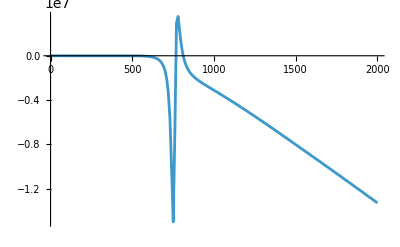

```mathematica
ListLinePlot[Impart]
```

```mathematica
rho=-1/π*Im1/((Re1+mr2)^2+Im1^2);
```

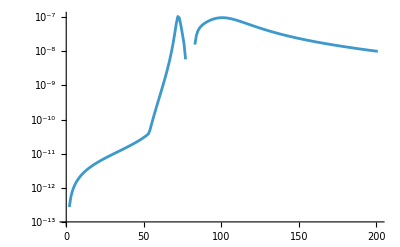

```mathematica
ListLinePlot[rho,ScalingFunctions->"Log"]
```

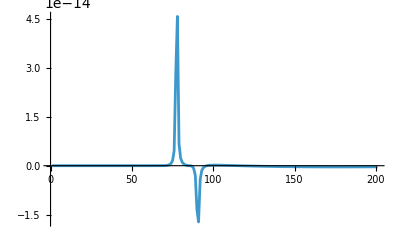

```mathematica
ListLinePlot[rho,PlotRange->All]
```

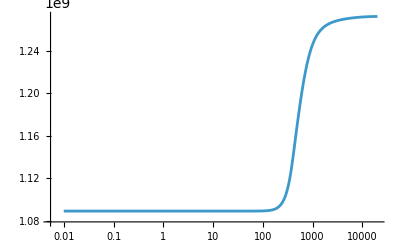

```mathematica
k=Flatten[Import["kMeV.dat"]];
mrho2=Flatten[Import["mrho2.dat"]];
re=Flatten[Import["gammarho_Re.dat"]];
ListLinePlot[Transpose[{k,mrho2}],ScalingFunctions->{"Log",Automatic}]
```

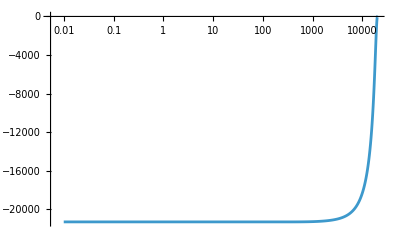

```mathematica
ListLinePlot[Transpose[{k,re}],ScalingFunctions->{"Log",Automatic}]
```